Jonas Neundorf, Jan Skottke

# Blatt 7

Definieren wir zunächst die Konstanten.

```mathematica
constants = {Subscript[μ, 0]-> 4*Pi*10^-7}
```

{μ_0→π/2500000}

Allgemein gilt für das Magnetfeld eines geraden Leiters im Vakuum

```mathematica
B[r_] = (Subscript[μ, 0]* i)/(2*Pi*r)
```

(i μ_0)/(2 π r)

wobei i die Stromstärke bezeichent. In kartesischen Koordinaten ausgedrückt ist das (habe was geändert)

```mathematica
B[x_, y_] = B[Sqrt[x^2+ y^2]] * {y/Sqrt[x^2+ y^2], -x/Sqrt[x^2+ y^2]}
```

{(i y μ_0)/(2 π (x^2+y^2)),-(i x μ_0)/(2 π (x^2+y^2))}

Anmerkung : das ist leider falsch. Die x-Komponente ist prop. y, die y Komponente proportional x.

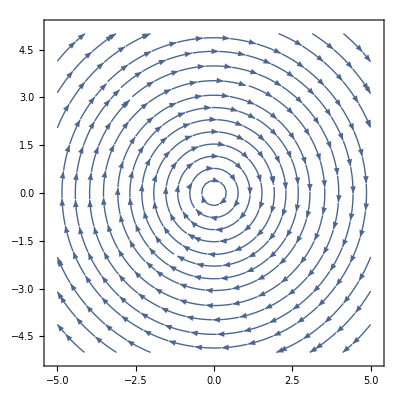

```mathematica
StreamPlot[Evaluate[B[x,y] /. constants /. i->1],{x,-5,5},{y,-5,5}]
```

Anmerkung : sieht mehr nach Punktladung als nach Kreisförmigen Feldlinien aus...

Diese Formeln gehen davon aus, dass sich der Leiter im Ursprung befindet. Befindet er sich nicht dort, sondern an einem Punkt {x_p, y_p}, so wird daraus

```mathematica
B[x_, y_, xp_, yp_] = B[x - xp, y - yp]
```

{(i (y-yp) μ_0)/(2 π ((x-xp)^2+(y-yp)^2)),-(i (x-xp) μ_0)/(2 π ((x-xp)^2+(y-yp)^2))}

Die Leiter befindet sich auf der kreisförmigen Hülle des Strahlrohres. Sie sollen symmetrisch um die y=0-Ebene angeordnet sein und auf jeder Seite den Winkel ϕ in gleichen Abständen einnehmen.

```mathematica
multiConductorField[ϕmax_, nCond_, x_, y_, R_] := Module[{Δϕ, ϕ, xp, yp},
Δϕ = (2*ϕmax)/nCond;
xp := R*Cos[ϕ];
yp := R*Sin[ϕ];
Return[Sum[B[x, y,xp, yp] -B[x, y, -xp, -yp], {ϕ, (- ϕmax)/2, ϕmax/2, Δϕ}]];
]
```

Plotten wir nun dieses Feld und setzen dazu R fest.

```mathematica
Rfix = 0.02
```

0.02

Mit dem Manipulate brauch es immer etwas bis Mathematica einen neuen Plot macht.

```mathematica
Manipulate[StreamPlot[multiConductorField[f,20, x, y, Rfix] //.constants /. i-> 12000, {x, -Rfix, Rfix}, {y, -Rfix, Rfix}, Axes->True,AxesLabel->{"B_x","B_y"}],{f,0,2*Pi,Pi/4}]
```

Ok, die Norm, und somit auch das Refine, können wir weg lassen. Wir brauchen lediglich die erste Komponente aus deiner Methode:

```mathematica
Plot[SeriesCoefficient[1/Norm[multiConductorField[π/4, 20, 0, 0, Rfix]]*(Rfix)^(n-1)*multiConductorField[Pi/4, 20, x, 0, Rfix][[2]]//.constants//.i-> 12000,{x,Rfix,n}],{n,0,90}]
```

-Graphics-

Anmerkung : wie auf dem Blatt gesagt, Sie sollten erstmal das was in die SeriesCoefficients kommt komplett mit Konstanten auswerten lassen. Sonst rechnet sich das tot. Und was das Refine[Norm...  hier soll ist mir unklar.

```mathematica
SeriesCoefficient[1/Norm[multiConductorField[π/4, 20, 0, 0, Rfix]]*(Rfix)^(n-1)*multiConductorField[Pi/4, 20, x, 0, Rfix][[2]]//.constants//.i-> 12000,{x,0,n}] /.n->2
```

38.3938

```mathematica
o
```

o

```mathematica
Series[Rfix^(n-1)/Norm[multiConductorField[π/4, 20, 0, 0, Rfix]]*multiConductorField[Pi/4, 20, x, 0, Rfix][[2]]//.constants//.i-> 12000, {x, 0, 5}]
```

50. 0.02^n+1.73519×10^-14 0.02^n x+95984.6 0.02^n x^2+3.55366×10^-11 0.02^n x^3+1.24896×10^8 0.02^n x^4-8.73348×10^-7 0.02^n x^5+O[x]^6

```mathematica
multiConductorField[π/4, 20, 0, 0, Rfix] //.constants //.i-> 12000
```

{1.33934×10^-17,2.55932}